# Figure 6

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{RGBColor[1,(2 t)^3,(2 t)^3],0<=t<=1/2},{RGBColor[(1-2 (t-1/2)),(1-2 (t-1/2)),1],1/2<t<=1}}];
```

All data were generated with julia code https : // github . com/djuliannader/RabiModel . git

## Time-dependent term ~σ_z

#### Negativity

```mathematica
Datneg={{1.43765,0.10213964004409326},{1.4378,0.006180404397177375},{1.438,0.0007185854186317897},{1.44,9.813615404496989*10^-5},{1.8,0.0037534943181130043},{2,0.0036342628098346985},{2.16,0.0014794895509175898},{2.17,0.005929708605961537},{2.171,0.01629766138316424},{2.172,0.08141534340153678},{2.173,0.5219203964998027},{2.174,0.042022232243011715},{2.175,0.009925687096497882},{2.176,0.0034962468907218103},{2.177,0.0015269944032589855},{2.178,0.0006667513587870211},{2.179,0.00031689696489678454},{2.18,0.00017432542044582},{2.19,1.2591*10^-5},{2.2,2.516524*10^-5},{2.3,0.003994306117855784},{2.4,0.0038692193124505447},{2.6,0.003728521712607291},{2.8,0.0036380677722100963},{3,0.0035305723949896617},{3.2,0.003403702857674995},{3.4,0.0032329925106564517},{3.6,0.0029887771724737},{3.8,0.002611042726570423},{4,0.0019907103157235095},{4.05,0.0017545368415605722},{4.1,0.0014758260442511162},{4.15,0.001181909944742321},{4.2,8.945691*10^-5},{4.21,0.003123400225836024},{4.22,0.001039707257270761},{4.23,0.007688159169442876},{4.24,0.00497444339962283},{4.25,0.012846634068778284},{4.26,0.05045177417112745},{4.27,0.0346524610682164},{4.28,0.20363517697743472},{4.29,0.15008163422405985},{4.3,0.1558113308797553},{4.31,0.5748690496110065},{4.32,0.43975991527245495},{4.33,0.3119883911000165},{4.34,0.4721643804540283},{4.35,0.7227049848716758},{4.36,0.4681091606950456},{4.37,0.3714889955785583},{4.38,0.39055046302023366},{4.39,0.46268646059985086},{4.4,0.3002622904372383},{4.45,0.007554379743763606},{4.5,0.0004987800772968676},{4.55,0.000159747990006065},{4.6,0.000190843444878519},{4.65,9.726027*10^-5},{4.7,0.00018524700965505403},{4.75,0.00037475208156068085},{4.8,0.0004707097392422366},{4.85,0.0005168751356214862},{4.9,0.0005550700117313845},{4.95,0.0005871766616005747},{5,0.0006145307951188617},{5.1,0.0006448748561624917},{5.2,0.000677354908038108},{5.4,0.000645229037751438},{5.6,0.0006372058093395694},{5.8,0.0006202142452862436},{6,0.0006369563026660252},{6.2,0.0006497895093662276},{6.4,0.0006595137199021384},{6.6,0.000669379878651899},{6.8,0.000675092827463919},{7,0.00068008890510729},{7.2,0.0006839823871827022},{7.4,0.0006867776513899138},{7.6,0.0006883958741890073},{7.8,0.00068856407101614},{8,0.0006866059038055372},{8.2,0.0006807748306121297},{8.4,0.0006654455606480703},{8.6,0.0006103246580499988},{8.65,0.0006116795388300122},{8.7,0.00024625038603198757},{8.75,0.0007065867215267918},{8.76,0.027337669608767712},{8.768,0.22844386271153594},{8.77,0.08581217166627497},{8.78,0.00140630680043774},{8.79,0.0007204460138958702},{8.8,0.0017021458338943862},{8.85,0.0033576011252822724},{8.9,0.0038209695390944987},{9,0.004185613102762886},{9.2,0.004394607558311225},{9.4,0.004467410594464649},{9.6,0.004501826842757239},{10.2,8.024916131610382*10^-7}};
Datnegp={{1.43765,3.261307215840503*10^-6},{1.438,0.0007185854186317897},{1.44,9.813615404496989*10^-5},{1.8,0.0037534943181130043},{2,0.0036342628098346985},{2.16,0.0014794895509175898},{2.17,7.347493389375792*10^-5},{2.172,7.213063378808116*10^-5},{2.173,8.497478380831147*10^-5},{2.175,6.496302922709418*10^-5},{2.18,5.6313373584471194*10^-5},{2.19,1.2591*10^-5},{2.2,2.516524*10^-5},{2.3,0.003994306117855784},{2.4,0.0038692193124505447},{2.6,0.003728521712607291},{2.8,0.0036380677722100963},{3,0.0035305723949896617},{3.2,0.003403702857674995},{3.4,0.0032329925106564517},{3.6,0.0029887771724737},{3.8,0.002611042726570423},{4,0.0019907103157235095},{4.05,0.0017545368415605722},{4.1,0.0014758260442511162},{4.15,0.001181909944742321},{4.2,8.945691*10^-5},{4.21,0.003123400225836024},{4.22,0.001039707257270761},{4.23,0.0033715363902164786},{4.24,0.007835094025814948},{4.25,0.01591335598839505},{4.26,0.02794978818637217},{4.27,0.04815203896119358},{4.28,0.08549115268450791},{4.29,0.1429435015749021},{4.30,0.22618944954194053},{4.31,0.3247642492130247},{4.32,0.4162235802272496},{4.33,0.4923794989080075},{4.34,0.5629516802385026},{4.35,0.6205210740030522},{4.36,0.6306692977216712},{4.37,0.606949400791809},{4.38,0.5859402092704675},{4.39,0.5513342562088359},{4.4,0.48317708943394044},{4.45,0.01493156195603662},{4.5,0.0003469503399062823},{4.55,2.3129758737194805*10^-6},{4.6,9.560617966308804*10^-6},{4.6,0.000190843444878519},{4.65,9.726027*10^-5},{4.7,0.00018524700965505403},{4.75,0.00037475208156068085},{4.8,0.0004707097392422366},{4.85,0.0005168751356214862},{4.9,0.0005550700117313845},{4.95,0.0005871766616005747},{5,0.0006145307951188617},{5.1,0.0006448748561624917},{5.2,0.000677354908038108},{5.4,0.000645229037751438},{5.6,0.0006372058093395694},{5.8,0.0006202142452862436},{6,0.0006369563026660252},{6.2,0.0006497895093662276},{6.4,0.0006595137199021384},{6.6,0.000669379878651899},{6.8,0.000675092827463919},{7,0.00068008890510729},{7.2,0.0006839823871827022},{7.4,0.0006867776513899138},{7.6,0.0006883958741890073},{7.8,0.00068856407101614},{8,0.0006866059038055372},{8.2,0.0006807748306121297},{8.4,0.0006654455606480703},{8.6,0.0006103246580499988},{8.65,0.0006116795388300122},{8.7,0.00024625038603198757},{8.75,3.132105348191416*10^-5},{8.76,1.0960241315194352*10^-5},{8.768,1.0797373786175513*10^-5},{8.77,1.3122920473618294*10^-5},{8.78,0.00140630680043774},{8.79,0.0007204460138958702},{8.8,0.0017021458338943862},{8.85,0.0033576011252822724},{8.9,0.0038209695390944987},{9,0.004185613102762886},{9.2,0.004394607558311225},{9.4,0.004467410594464649},{9.6,0.004501826842757239},{10.2,8.024916131610382*10^-7}};
Datnegpbl={{4,5.668494811717906*10^-6},{4.1,2.882826706131774*10^-5},{4.2,0.001221733083990481},{4.24,0.0034582950463444696},{4.28,0.0537372795190483},{4.32,0.2878844162929507},{4.36,0.4687374237628193},{4.4,0.376171565648324},{4.45,0.01158463784793704},{4.5,9.198797778600062*10^-6}};
```

```mathematica
exres=8.801011;
Dataneg=Table[{Datneg[[i,1]]/exres,Datneg[[i,2]]},{i,1,Length[Datneg]}];
Datanegp=Table[{Datnegp[[i,1]]/exres,Datnegp[[i,2]]},{i,1,Length[Datnegp]}];
Datanegpbl=Table[{Datnegpbl[[i,1]]/exres,Datnegpbl[[i,2]]},{i,1,Length[Datnegpbl]}];
```

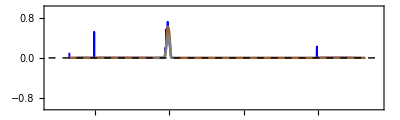

```mathematica
figzoomin=Show[ListPlot[{Dataneg,Datanegp,Datanegpbl},Joined->True,
PlotStyle->{{Blue,Thickness[0.0035]},{Brown,Thickness[0.0042]},{Gray,Thickness[0.0045]}},PlotRange->{{0.1,1.2},{-1,1}},GridLines->{{1/6,1/4,1/2,1},{}},GridLinesStyle->{{Red,Dashed},{}},Axes->False,Frame->True,LabelStyle->{10,Black}],Plot[0,{x,0,1.2},PlotStyle->{Black,Dashed,Thick}],AspectRatio->0.3,ImageResolution->500]
```

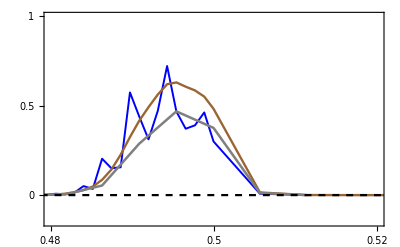

```mathematica
figzoominres=Show[ListPlot[{Dataneg,Datanegp,Datanegpbl},Joined->True,
PlotStyle->{{Blue,Thickness[0.0035]},{Brown,Thickness[0.0042]},{Gray,Thickness[0.0045]}},PlotRange->{{0.48,0.52},{-0.15,1}},GridLines->{{1/6,1/4,1/2,1},{}},FrameTicks->{{{0,0.5,1},None},{{0.48,0.5,0.52},None}},GridLinesStyle->{{Red,Dashed},{}},Axes->False,Frame->True,LabelStyle->{9.5,Black}],Plot[0,{x,0,1.2},PlotStyle->{{Black,Dashed}}],ImageResolution->500]
```

```mathematica
datawigner=Import["Data/wigner_Floquet8.dat"];
datawignern={};
Do[If[datawigner[[i,3]]<0,AppendTo[datawignern,{datawigner[[i,1]],datawigner[[i,2]],2*datawigner[[i,3]]}],AppendTo[datawignern,{datawigner[[i,1]],datawigner[[i,2]],datawigner[[i,3]]}]],{i,1,Length[datawigner]}]
```

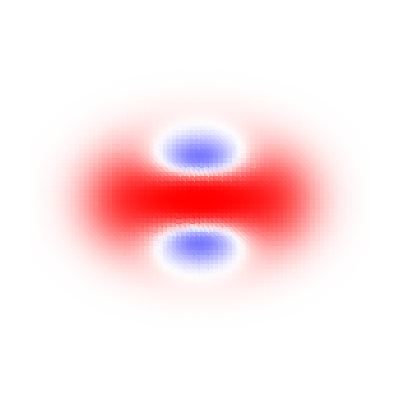

```mathematica
fac=0.5/0.35;
wigner8=Show[ListDensityPlot[datawignern,PlotRange->{{-0.5,0.5},{-0.5,0.5},All},Frame->False,Axes->False,ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)]]
```

```mathematica
Reswig=Show[figzoomin,Graphics@Inset[wigner1,{0.1,0.45},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner2,{0.3,0.06},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner3,{0.35,-0.8},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner4,{0.38,0.4},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner5,{0.54,0.35},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner6,{0.75,0.3},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner7,{0.88,0.34},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner8,{1.06,0.24},{Left,Bottom},Scaled[0.25]],Graphics@Inset[figzoominres,{0.6,-0.9},{Left,Bottom},Scaled[0.45]],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.14,0.5},{1.43765/exres,0.1}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.3,0.36},{2.173/exres,0.52}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.39,-0.45},{3.4/exres,0.0}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.43,0.5},{4.28/exres,0.2}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.55,0.6},{4.32/exres,0.44}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.78,0.4},{6.6/exres,0.0}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.95,0.4},{8.76/exres,0.03}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{1.07,0.4},{8.768/exres,0.23}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.59,-0.4},{0.52,-0.15}}]}]]
```

## Time-dependent term ~σ_x

#### Negativity

```mathematica
DatnegSigx={{1.2,2*10^(-5)},{1.3,0.003966515599469034},{1.4,0.003965817376120784},{1.5,0.003964924087231481},{1.6,0.003963364090642907},{1.7,0.003909606028812407},{1.72,0.003925244876849421},{1.73,0.03944507160561361},{1.74,0.003977897697708066},{1.8,0.00396639486464978},{1.9,0.003963454432205138},{2,0.0039613671201674805},{2.1,0.003958830345039965},{2.2,0.003956612249071068},{2.3,0.0039525646657998514},{2.4,0.003946825536048859},{2.5,0.0039375704225455},{2.6,0.00391898322629336},{2.7,0.003875382034446151},{2.8,0.0037057069063866077},{2.82,0.0008567825363094972},{2.84,0.00011809784291183512},{2.86,0.00014667449721383896},{2.88,0.010065643177876726},{2.9,0.0878527403842233},{2.91,0.18250605433669698},{2.92,0.007654153308507716},{2.94,0.0035964184261123577},{2.96,0.003776618228757078},{2.98,0.0038619109764730375},{3,0.0039027034318037668},{3.1,0.0039518982517277035},{3.2,0.003955460981474035},{3.3,0.003953657967800783},{3.4,0.003950756922670884},{3.5,0.003947491125735558},{3.6,0.00394397132661739},{3.7,0.003940057725303481},{3.8,0.003935762137799781},{3.9,0.003930694186676353},{4,0.0039243962061221715},{4.1,0.003915663498299526},{4.2,0.0039000886012465763},{4.3,0.0038308978958370155},{4.4,0.0039822686020554166},{4.5,0.003933935453179549},{4.6,0.003917483401714605},{4.7,0.0039054349782274844},{4.8,0.0038942298546025267},{4.9,0.0038827655056430377},{5,0.0038705186154008864},{5.1,0.0038571794168185125},{5.2,0.003840498811015003},{5.3,0.003825466420053214},{5.4,0.0038069341803266266},{5.5,0.003786020078317076},{5.6,0.0037623859943016758},{5.7,0.0037367102563625743},{5.8,0.003710042857482776},{5.9,0.003675125752587549},{6,0.00363531173496745},{6.1,0.0035873726629809255},{6.2,0.003535406363292859},{6.3,0.0034757174149229186},{6.4,0.0034333820884930866},{6.5,0.003361737918070151},{6.6,0.003245391556755406},{6.7,0.003152863589660937},{6.8,0.0030307608693009858},{6.9,0.0028876097459114014},{7,0.0027200769939919045},{7.1,0.0025223765523492148},{7.2,0.002290841446011882},{7.3,0.0020196225167994353},{7.4,0.0017071246952631292},{7.5,0.0013402291646544828},{7.6,0.0009199576918721419},{7.7,0.000445723234276052},{7.8,7*10^(-6)},{7.9,0.00048774302836385175},{8,0.0004557819256876261},{8.1,0.003406471676911549},{8.2,0.9673614372389265},{8.3,1.52149433609411},{8.4,0.011402925723104973},{8.5,0.004978853303621911},{8.6,0.0018528764058474145},{8.7,0.00016324324110272848},{8.8,0.0010662009875987977},{8.9,3.500634423936333^-5},{9,0.008419403993106922},{9.1,0.003602302195180096},{9.2,0.0019272556768779037},{9.4,0.011053170701234238},{9.6,9.410953894350982*10^-5},{9.8,1.6931583283641416*10^-5},{10,1.8246867544924328*10^-5},{10,3.766101601598848*10^-5}};
DatnegpSigx={{1.2,2*10^(-5)},{1.3,0.003966515599469034},{1.4,0.003965817376120784},{1.5,0.003964924087231481},{1.6,0.003963364090642907},{1.7,0.003909606028812407},{1.72,0.003925244876849421},{1.73,3.41742783149801*10^-6},{1.74,0.003977897697708066},{1.8,0.00396639486464978},{1.9,0.003963454432205138},{2,0.0039613671201674805},{2.1,0.003958830345039965},{2.2,0.003956612249071068},{2.3,0.0039525646657998514},{2.4,0.003946825536048859},{2.5,0.0039375704225455},{2.6,0.00391898322629336},{2.7,0.003875382034446151},{2.8,0.0037057069063866077},{2.82,0.0008567825363094972},{2.84,0.00011809784291183512},{2.86,0.00014667449721383896},{2.88,0.010065643177876726},{2.89,0.017502808550053928},{2.90,0.02019425235082606},{2.905,0.019637743800535956},{2.91,0.01775583899812161},{2.911,},{2.92,0.011139008790546745},{2.94,0.0035964184261123577},{2.96,0.003776618228757078},{2.98,0.0038619109764730375},{3,0.0039027034318037668},{3.1,0.0039518982517277035},{3.2,0.003955460981474035},{3.3,0.003953657967800783},{3.4,0.003950756922670884},{3.5,0.003947491125735558},{3.6,0.00394397132661739},{3.7,0.003940057725303481},{3.8,0.003935762137799781},{3.9,0.003930694186676353},{4,0.0039243962061221715},{4.1,0.003915663498299526},{4.2,0.0039000886012465763},{4.3,0.0038308978958370155},{4.4,0.0039822686020554166},{4.5,0.003933935453179549},{4.6,0.003917483401714605},{4.7,0.0039054349782274844},{4.8,0.0038942298546025267},{4.9,0.0038827655056430377},{5,0.0038705186154008864},{5.1,0.0038571794168185125},{5.2,0.003840498811015003},{5.3,0.003825466420053214},{5.4,0.0038069341803266266},{5.5,0.003786020078317076},{5.6,0.0037623859943016758},{5.7,0.0037367102563625743},{5.8,0.003710042857482776},{5.9,0.003675125752587549},{6,0.00363531173496745},{6.1,0.0035873726629809255},{6.2,0.003535406363292859},{6.3,0.0034757174149229186},{6.4,0.0034333820884930866},{6.5,0.003361737918070151},{6.6,0.003245391556755406},{6.7,0.003152863589660937},{6.8,0.0030307608693009858},{6.9,0.0028876097459114014},{7,0.0027200769939919045},{7.1,0.0025223765523492148},{7.2,0.002290841446011882},{7.3,0.0020196225167994353},{7.4,0.0017071246952631292},{7.5,0.0013402291646544828},{7.6,0.0009199576918721419},{7.7,0.000445723234276052},{7.8,7*10^(-6)},{7.9,3.6487318577638206*10^-6},{8.0,1.1089280018361514*10^-5},{8.1,0.002215313778017869},{8.15,0.08938462490170407},{8.2,0.9656477875109526},{8.25,2.8018756347109783},{8.3,2.26784733783828},{8.35,1.0436079664713258},{8.4,1.6177425940710943},{8.45,2.3155028607124604},{8.5,1.4327991503771105},{8.55,0.9153027090010817},{8.6,1.2187640289206043},{8.65,1.1564079476434976},{8.7,0.6558517400460688},{8.75,0.2911652212346991},{8.8,0.1461602868393952},{8.85,0.1461602868393952},{8.9,0.07930578098981056},{8.95,0.03261686426531418},{9,0.0009790858447671358},{9.1,0.003602302195180096},{9.2,0.0019272556768779037},{9.4,0.011053170701234238},{9.6,9.410953894350982*10^-5},{9.8,1.6931583283641416*10^-5},{10,1.8246867544924328*10^-5},{10,3.766101601598848*10^-5}};
DatnegpSigxbl={{8.05,0.012590564578851974},{8.15,0.10448511100607612},{8.20,0.4065266223009238},{8.25,0.7474044967195376},{8.3,0.29134143923145067},{8.35,0.09624657434738454},{8.45,0.2399980400622038},{8.55,0.03434288528770892},{8.65,0.18613343028820659},{8.75,0.04215690524558378},{8.85,0.0161804103431332},{8.95,0.0}};
```

```mathematica
exres=8.801011;
DatanegSigx=Table[{DatnegSigx[[i,1]]/exres,DatnegSigx[[i,2]]},{i,1,Length[DatnegSigx]}];
DatanegpSigx=Table[{DatnegpSigx[[i,1]]/exres,DatnegpSigx[[i,2]]},{i,1,Length[DatnegpSigx]}];
DatanegpSigxbl=Table[{DatnegpSigxbl[[i,1]]/exres,DatnegpSigxbl[[i,2]]},{i,1,Length[DatnegpSigxbl]}];
```

```mathematica
figzoominsigx=Show[ListPlot[{DatanegSigx,DatanegpSigx,DatanegpSigxbl},Joined->True,
PlotStyle->{{Blue,Thickness[0.0035]},{Brown,Thickness[0.004]},{Gray,Thickness[0.0045]}},PlotRange->{{0.05,1.2},{-1.6,3}},GridLines->{{1/3,1/5,1},{}},GridLinesStyle->{{Darker[Green],Dashed},{}},Axes->False,Frame->True,LabelStyle->{10,Black}],Plot[0,{x,0,1.2},PlotStyle->{Black,Dashed,Thick}],AspectRatio->0.3,ImageResolution->500]
```

-Graphics-

```mathematica
datawigner=Import["Data/wigner_Floquet5_sigx.dat"];
datawignern={};
Do[If[datawigner[[i,3]]<0,AppendTo[datawignern,{datawigner[[i,1]],datawigner[[i,2]],2*datawigner[[i,3]]}],AppendTo[datawignern,{datawigner[[i,1]],datawigner[[i,2]],datawigner[[i,3]]}]],{i,1,Length[datawigner]}]
```

```mathematica
fac=0.5/0.35;
wigner5sigx=Show[ListDensityPlot[datawignern,PlotRange->{{-1.25,1.25},{-1.25,1.25},All},Frame->False,Axes->False,ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)]]
```

-Graphics-

```mathematica
Reswig=Show[figzoominsigx,Graphics@Inset[wigner1sigx,{0.07,0.52},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner2sigx,{0.38,0.45},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner3sigx,{0.39,-1.25},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner4sigx,{0.74,0.1},{Left,Bottom},Scaled[0.35]],Graphics@Inset[wigner5sigx,{0.82,-1.35},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner6sigx,{1.05,0.7},{Left,Bottom},Scaled[0.25]],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.14,0.6},{1.73/exres,0.04}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.4,0.6},{2.91/exres,0.18}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.45,-0.6},{4.4/exres,0.0}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.84,0.8},{8.2/exres,0.97}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.9,-0.6},{8.4/exres,0.01}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{1.1,0.8},{9.6/exres,0.0}}]}]]
```

-Graphics-